```mathematica
(* 01 *)
Factor[x^3+3 x^2+x+3]
```

(3+x) (1+x^2)

```mathematica
(* 02 *)
TraditionalForm[Factor[x^3+3 x^2+x+3]]
```

(x+3) (x^2+1)

```mathematica
(* 03 *)
```

{{x→-8},{x→1}}

```mathematica
(* 04 *)
```

{{x→35/11,y→-21/11}}

```mathematica
(* 05 *)
N[%,10]
```

{{x→3.18182,y→-1.90909}}

```mathematica
(* 06 *)
Solve[x^2+5x+9==14]
```

{{x→1/2 (-5-3 √5)},{x→1/2 (-5+3 √5)}}

```mathematica
(* 07 *)
result = x/. Solve[x^2+5x+9==14]
```

{1/2 (-5-3 √5),1/2 (-5+3 √5)}

```mathematica
Last[result]
```

1/2 (-5+3 √5)

```mathematica
(* 08 *)
N[result,4]
```

{-5.854,0.8541}

```mathematica
(* 09 *)
Reduce[3 x^4-5 y^3==11]
```

x==-((11+5 y^3)^(1/4))/3^(1/4)||x==-(ⅈ (11+5 y^3)^(1/4))/3^(1/4)||x==(ⅈ (11+5 y^3)^(1/4))/3^(1/4)||x==((11+5 y^3)^(1/4))/3^(1/4)

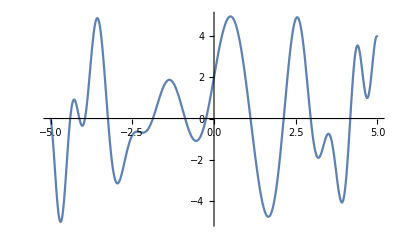

```mathematica
(* 10 *)
Plot[3Sin[3x]+2Cos[x^2],{x,-5,5}]
```

```mathematica
FindRoot[3Sin[3x]+2Cos[x^2],{x,0}]
```

{x→-0.242726}